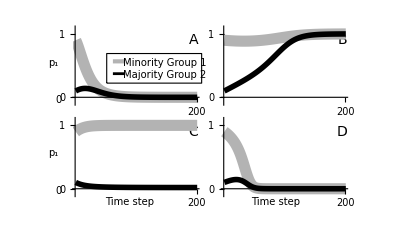

~/Fig3.pdf

```mathematica
(*Makes figures 2, 3, and 4 in the manuscript. Running figure 2 is fast. Running figures 3 and 4 can with the current parameterizations can take several hours*)


Clear[wik,wnik, Rk, Rik, Vk, Vik, boundsim,a,m,d,g,mu];

(*simulation function*)
boundsim[
pg1init_,(*(vector) group 1: norm 0, norm 1*)
pg2init_,(*(vector) group 2: norm 0, norm 1*)
tmax_,(*# sims*)
a_,(*prob of assorting on marker*)
m_,(*(vector) proportion of each group that is visitors*)
d_,(*(matrix) relative group sizes: how many times bigger the row group is than the column group*)
g_,(*(vector) inter-ethnic coordination payoff bonus for each group*)
mu_ (*effect of a payoff difference on copying*)
]:=Module[{},

(*intialize vectors and matrices*)
p1={pg1init[[1]], pg2init[[1]]}; (*norm 0 in both groups*)
p2={pg1init[[2]], pg2init[[2]]}; (*norm 1 in both groups*)
matg1all={pg1init}; (*matrix holding norm freqs for group 1*)
matg2all={pg2init};
fitg1={1,1}; (*fitness of norms in group 1*)
fitg2={1,1};
fitg1all={fitg1}; (*matrix holding norm fitnesses for group 1*)
fitg2all={fitg2};

(*generalized fitness*)
Rk=(1-mk)+dnk*mnk;
Rik=pik*(1-mk)+pink*dnk*mnk;
Vk=mk+dnk*(1-mnk);
Vik=pik*mk+pink*dnk*(1-mnk);

fitnessik=a*((1-mk)*1/Rik*(pink*dnk*mnk*(1+gk)+pik*(1-mk)*1)+mk*1/Vik*(pink*dnk*(1-mnk)*(1+gk)+pik*mk*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+pik*mk*1));


(*new phenotype freqs after copying*)
pikprime=pik+pik*pnik*mu*(wik-wnik);


(*simulation*)
For    [t=1,t<=tmax,t++,

(*update norm frequencies for the two groups*)
p1k=p1;
p2k=p2;

For[k=1,k≤2,k++,(*loop over groups*)

If[k==1,nk=2,nk=1]; (*adjust index of other group*)


(*phenotype fitnesses*)

If[p1k=={0,0},
w1k=0,
w1k=fitnessik/.{
dnk->d[[nk,k]],gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p1k[[k]],pink->p1k[[nk]]
}
];

If[p1k=={0,0},
w1nk=0,
w1nk=fitnessik/.{
dnk->d[[k,nk]],gk->g[[nk]],
mk->m[[nk]],mnk->m[[k]],
pik->p1k[[nk]],pink->p1k[[k]]
}
];

If[p2k=={0,0},
w2k=0,
w2k=fitnessik/.{
dnk->d[[nk,k]],gk->g[[k]],
mk->m[[k]],mnk->m[[nk]],
pik->p2k[[k]],pink->p2k[[nk]]
}
];

If[p2k=={0,0},
w2nk=0,
w2nk=fitnessik/.{
dnk->d[[k,nk]],gk->g[[nk]],
mk->m[[nk]],mnk->m[[k]],
pik->p2k[[nk]],pink->p2k[[k]]
}
];


(*Recursion*)
p1kprime=pikprime /.
{pik->p1k[[k]],
pnik->p2k[[k]],
wik->w1k,
wnik->w2k};

p2kprime=1-p1kprime;


(*update phenotype and fitness matrices*)
If [k==1,
{
p1={p1kprime,p1[[2]]}, (*just update freq of norm 0 for group 1*)
p2={p2kprime,p2[[2]]},(*just norm 1 for group 1*)
fitg1={w1k,w2k}
},
{
p1 = {p1[[1]], p1kprime},
(*just update freq of norm 0 for group 2*)
p2 = {p2[[1]], p2kprime},(*just norm 1 for group 2*)
fitg2={w1k,w2k}
}
](*if/else*)

];(*for k*)


(*accumulate phenotype freqs and fitnesses across sims*)
matg1all=Join[matg1all,{{p1[[1]],p2[[1]]}}];
matg2all=Join[matg2all,{{p1[[2]],p2[[2]]}}];
fitg1all=Join[fitg1all, {fitg1}];
fitg2all=Join[fitg2all, {fitg2}];

](*for t*)

];(*boundsim*)



(*function for solving the model numerically*)
boundsolve[
a_,(*prob of assorting on marker*)
m_,(*(vector) proportion of each group that is visitors*)
d_,(*(matrix) relative group sizes: how many times bigger the row group is than the column group*)
g_,(*(vector) inter-ethnic coordination payoff bonus for each group*)
mu_ (*effect of a payoff difference on copying*)
]:=Module[{},

Clear[p11,p12];

p11;(*freq of each norm in each group*)
p12; 
(*p21=1-p11;
p22=1-p12;*)

m1=m[[1]];
m2=m[[2]];
d1=d[[1,2]];
d2=d[[2,1]];
g1=g[[1]];
g2=g[[2]];


(*generalized fitness*)
Rk=(1-mk)+dnk*mnk;
Rik=pik*(1-mk)+pink*dnk*mnk;
Vk=mk+dnk*(1-mnk);
Vik=pik*mk+pink*dnk*(1-mnk);

fitnessik=a*((1-mk)*1/Rik*(pink*dnk*mnk*(1+gk)+pik*(1-mk)*1)+mk*1/Vik*(pink*dnk*(1-mnk)*(1+gk)+pik*mk*1))+(1-a)*((1-mk)*1/Rk*(pink*dnk*mnk*(1+gk)+pik*(1-mk)*1)+mk*1/Vk*(pink*dnk*(1-mnk)*(1+gk)+pik*mk*1));


(*new phenotype freqs after copying*)
pikprime=pik+pik*pnik*mu*(wik-wnik);


(*phenotype fitnesses*)
w11=fitnessik/.{
dnk->d2,gk->g1,
mk->m1,mnk->m2,
pik->p11,pink->p12
};

w12=fitnessik/.{
dnk->d1,gk->g2,
mk->m2,mnk->m1,
pik->p12,pink->p11
};

w21=fitnessik/.{
dnk->d2,gk->g1,
mk->m1,mnk->m2,
pik->1-p11,pink->1-p12
};

w22=fitnessik/.{
dnk->d1,gk->g2,
mk->m2,mnk->m1,
pik->1-p12,pink->1-p11
};


(*Recursions*)
p11prime=pikprime /.
{pik->p11,
pnik->1-p11,
wik->w11,
wnik->w21};

p21prime=1-p11prime;

p12prime=pikprime /.
{pik->p12,
pnik->1-p12,
wik->w12,
wnik->w22};

p22prime=1-p12prime;


(*solve for equilibrium*)
solut=Solve[p11prime==p11&&
p12prime==p12 &&
0<=p11<=1 &&
0<=p12<=1,
{p11, p12},
Reals];

(*Print[solut];*)
Print[N[solut]];

points=Partition[{p11/.N[solut],p12/.N[solut]},2];
points=Flatten[points,1];
points=Transpose[points];
points=Partition[points,Length[solut]];
points=Transpose[points];

];(*boundsolve*)


(*Figure 3: plotting norm frequency trajectories*)

(*A*************************majority controls resources*******************************)

boundsim[
pg1init={0.9,0.1},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0.9, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];


(*
Print["Ending freq of norm 0 in both groups: ", p1,"

Matrices of norm freqs in each group: 
",
matg1all //MatrixForm,
matg2all //MatrixForm, "

Matrices of fitnesses of norms in each group:
",
fitg1all//MatrixForm,
fitg2all//MatrixForm
] 
*)

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3a=(*Labeled[*)
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{White,Black},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0"},{1,"1"}}}
];
(*
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True]
*)


(*B****************minority controlls resources*************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0.9, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.1,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];


(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)


(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3b=
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{White,White},
Ticks->{{{100,"",{0,0}},{200,"200",{0,0}}},{{0,"0",{0,0}},{1,"1",{0,0}}}}
];




(*C************************minority homeland*****************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0.7, (*prob of assorting on marker*)
m={0.1,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3c=
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{Black,Black},
Ticks->{{{100,""},{200,"200"}},{{0,"0"},{1,"1"}}}
];


(*D************************minority homeland, lots of visitors*****************************)
boundsim[
pg1init={0.9,0.1},  (*group 1: norm 0, norm 1*)
pg2init={0.1,0.9}, (*group 2: norm 0, norm 1*)

tmax =200, (*# sims*)

a=0.7, (*prob of assorting on marker*)
m={0.4,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];

(*
Print["
Beginning and ending norm freqs in group 1: 
",
matg1all[[1]],"
",
matg1all[[tmax+1]], "

Beginning and ending norm freqs in group 2:
",
matg2all[[1]],"
",
matg2all[[tmax+1]], "

Do norm freqs sum to one in group 1? 
",
Total[matg1all[[tmax+1]]], "

in group 2?
",
Total[matg2all[[tmax+1]]]
];
*)

(*Plots*)
p1g1=Take[matg1all[[All,1]],{1,tmax+1}];
p2g1=Take[matg1all[[All,2]],{1,tmax+1}];
p1g2=Take[matg2all[[All,1]],{1,tmax+1}];
p2g2=Take[matg2all[[All,2]],{1,tmax+1}];

Labeled[ListLinePlot[{p1g1,p2g1}, PlotLabel->"Group 1",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

Labeled[ListLinePlot[{p1g2,p2g2}, PlotLabel->"Group 2",
PlotLegends->{"norm 1", "norm 2"}],
{"Simulation", "Norm Frequency"},
{Bottom, Left}, RotateLabel -> True];

f3d=(*Labeled[*)
ListLinePlot[
{p1g1,p1g2}, (*PlotLabel->"Minority Norm 0",*)
(*PlotLegends->Placed[{"minority group 1", "majority group 2"},{Scaled[{0.5,0.5}],{0,0.5}}],*)
PlotRange->{{0,tmax},{-0.1,1.1}},
PlotStyle->{{GrayLevel[0.7], Thickness[0.02]},{Black, Thickness[0.01]}},
TicksStyle->{Black,White},
Ticks->{{{100,""},{200,"200"}},{{0,"0",{0,0}},{1,"1",{0,0}}}} (*{0,0} is tick length*)
];


(****************************************assemble plots into Fig 3*)
Fig3=Panel[
GraphicsGrid[
{{f3a,f3b},{f3c,f3d}},

Spacings->{
{
Scaled[0.4],
Scaled[0],
Scaled[0.2]
},
{
Scaled[0],
Scaled[0],
Scaled[0.3]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["A",14],{380,-45}],
Inset[Style["B",14],{740,-45}],
Inset[Style["C",14],{380,-270}],
Inset[Style["D",14],{740,-270}],
Inset[Style[Subscript[Style["p",Italic,10],Style["1",8]],Italic,10],{40,-100}],
Inset[Style[Subscript[Style["p",Italic,10],Style["1",8]],Italic,10],{40,-320}],
Inset[Style["Time step",10],{225,-440}],
Inset[Style["Time step",10],{580,-440}],
Inset[Style["0",10],{54,-190}],
Inset[Style["0",10],{54,-412}],

{EdgeForm[Thin],White,Rectangle[{170,-78},{400,-150}]},
Inset[Style["Minority Group 1",10],{310,-100}],
Inset[Style["Majority Group 2",10],{310,-130}],
{AbsoluteThickness[3],GrayLevel[0.7],Line[{{185,-97},{215,-97}}]},
{AbsoluteThickness[2],Black,Line[{{185,-127},{215,-127}}]}
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{0,5}}
](*panel*)


Export["~/Fig3.pdf",Fig3,"PDF"]
(*Export["/Users/johnbunce/Desktop/Fig3.pdf",Fig3,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
*)
```

Done part a

Done part b

Done part c

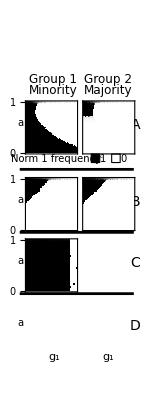

~/Fig2.pdf

```mathematica
(*Figure 2: Explore long-run trends*)
Clear[wik,wnik, Rk, Rik, Vk, Vik, a,m,d,g,mu];

aSeq=Range[0,1,0.01];(*prob of assorting on marker, change step size to 0.05 to make this run faster*)
gkSeq=Range[0,1,0.01];(*inter-ethnic coordination payoff bonus for each group, change step size to 0.05 to make this run faster*)
tmaxAll = 400;(*# sims, change this to something like 20 and it will run much faster*)
dAll={{1,0.5},{2,1}};
(*relative group sizes: how many times bigger the row group is than the column group*)
pg1initAll={0.9,0.1};(*group 1: norm 0, norm 1*)
pg2initAll={0.1,0.9};(*group 2: norm 0, norm 1*)


(*A********Low bidirectional visiting****************************************************)
Clear[grp1avec, grp2avec, grp1gmat, grp2gmat];
grp1avec=0;(*initialize vectors and matrices*)
grp2avec=0;
grp1gmat=ConstantArray[0,Length[aSeq]+1];
grp2gmat=ConstantArray[0,Length[aSeq]+1];

For    [gkInc=1,gkInc≤Length[gkSeq],gkInc++,
For    [aInc=1,aInc≤Length[aSeq],aInc++,

boundsim[
pg1init=pg1initAll,  
pg2init=pg2initAll, 

tmax =tmaxAll, 

a=aSeq[[aInc]], 
m={0.1,0.1},(*proportion of each group that is visitors*)
d=dAll,
g={gkSeq[[gkInc]],0.5},
mu=0.5(*effect of a payoff difference on copying*)
];

grp1avec=Flatten[{grp1avec, matg1all[[tmaxAll+1,1]]}];
(*Print["vec ", grp1avec];*)
grp2avec=Flatten[{grp2avec, matg2all[[tmaxAll+1,1]]}];

];(*For aInc*)

(*Print["join ",grp1gmat ," with vec ",grp1avec]; *)
grp1gmat=Flatten[{grp1gmat,grp1avec}];
(*Print["mat", grp1gmat];*)
grp2gmat=Flatten[{grp2gmat,grp2avec}];

grp1avec=0;(*re-initialize vectors*)
grp2avec=0;

]; (*For gkInc*)


matg1all[[tmaxAll+1]];
grp1gmat=Transpose[ArrayReshape[grp1gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp1gmat //MatrixForm;
grp1gmat=grp1gmat[[2 ;;,2;;]];(*delete junk row and column*)
grp1gmat //MatrixForm;


matg2all[[tmaxAll+1]];
grp2gmat=Transpose[ArrayReshape[grp2gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp2gmat //MatrixForm;
grp2gmat=grp2gmat[[2 ;;,2;;]]; (*delete junk row and column*)
grp2gmat //MatrixForm;


Labeled[ListLinePlot[{grp1gmat[[All,1]],
				grp1gmat[[All,3]],
				grp1gmat[[All,7]],
				grp1gmat[[All,11]],
				grp1gmat[[All,21]]}, 
PlotLabel->"Group 1 minority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


Labeled[ListLinePlot[{grp2gmat[[All,1]],
				grp2gmat[[All,3]],
				grp2gmat[[All,7]],
				grp2gmat[[All,11]],
				grp2gmat[[All,21]]}, 
PlotLabel->"Group 2 majority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


a1=(*Labeled[*)
ListDensityPlot[
1-grp1gmat, (*to reverse the color plotting scheme*)
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{0,1},None},{{{0,""},{1,""}},None}}
(*FrameLabel->{"","a"}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True
]*)


a2=(*Labeled[*)
ListDensityPlot[
1-grp2gmat,
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{0,""},{1,""}},None},{{{0,""},{1,""}},None}}
(*FrameLabel->{"",""}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*)

Print["Done part a"]


(*B**********High bidirectional visting***********************************************)
Clear[wik,wnik, Rk, Rik, Vk, Vik, a,m,d,g,mu];

(*
aSeq=Range[0,1,0.01];(*prob of assorting on marker*)
gkSeq=Range[0,1,0.01];(*inter-ethnic coordination payoff bonus for each group*)
(*tmaxAll = 20;(*# sims*)*)
dAll={{1,0.5},{2,1}};
(*relative group sizes: how many times bigger the row group is than the column group*)
pg1initAll={0.9,0.1};(*group 1: norm 0, norm 1*)
pg2initAll={0.1,0.9};(*group 2: norm 0, norm 1*)
*)

(*gnk=0.3, mk=mnk=1, dnk=2, mu=0.2*)
Clear[grp1avec, grp2avec, grp1gmat, grp2gmat];
grp1avec=0;(*initialize vectors and matrices*)
grp2avec=0;
grp1gmat=ConstantArray[0,Length[aSeq]+1];
grp2gmat=ConstantArray[0,Length[aSeq]+1];

For    [gkInc=1,gkInc≤Length[gkSeq],gkInc++,
For    [aInc=1,aInc≤Length[aSeq],aInc++,

boundsim[
pg1init=pg1initAll,  
pg2init=pg2initAll, 

tmax =tmaxAll, 

a=aSeq[[aInc]], 
m={0.4,0.4},(*proportion of each group that is visitors*)
d=dAll,
g={gkSeq[[gkInc]],0.5},
mu=0.5(*effect of a payoff difference on copying*)
];

grp1avec=Flatten[{grp1avec, matg1all[[tmaxAll+1,1]]}];
(*Print["vec ", grp1avec];*)
grp2avec=Flatten[{grp2avec, matg2all[[tmaxAll+1,1]]}];

];(*For aInc*)

(*Print["join ",grp1gmat ," with vec ",grp1avec]; *)
grp1gmat=Flatten[{grp1gmat,grp1avec}];
(*Print["mat", grp1gmat];*)
grp2gmat=Flatten[{grp2gmat,grp2avec}];

grp1avec=0;(*re-initialize vectors*)
grp2avec=0;

]; (*For gkInc*)


matg1all[[tmaxAll+1]];
grp1gmat=Transpose[ArrayReshape[grp1gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp1gmat //MatrixForm;
grp1gmat=grp1gmat[[2 ;;,2;;]];(*delete junk row and column*)
grp1gmat //MatrixForm;


matg2all[[tmaxAll+1]];
grp2gmat=Transpose[ArrayReshape[grp2gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp2gmat //MatrixForm;
grp2gmat=grp2gmat[[2 ;;,2;;]]; (*delete junk row and column*)
grp2gmat //MatrixForm;


Labeled[ListLinePlot[{grp1gmat[[All,1]],
				grp1gmat[[All,3]],
				grp1gmat[[All,7]],
				grp1gmat[[All,11]],
				grp1gmat[[All,21]]}, 
PlotLabel->"Group 1 minority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


Labeled[ListLinePlot[{grp2gmat[[All,1]],
				grp2gmat[[All,3]],
				grp2gmat[[All,7]],
				grp2gmat[[All,11]],
				grp2gmat[[All,21]]}, 
PlotLabel->"Group 2 majority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


b1=(*Labeled[*)
ListDensityPlot[
1-grp1gmat,
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{0,1},None},{{{0,""},{1,""}},None}}
(*FrameLabel->{"","a"}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*)


b2=(*Labeled[*)
ListDensityPlot[
1-grp2gmat,
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{0,""},{1,""}},None},{{{0,""},{1,""}},None}}
(*FrameLabel->{"",""}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*)

Print["Done part b"]


(*C*******Homeland low visiting*************************************************************)
Clear[wik,wnik, Rk, Rik, Vk, Vik, a,m,d,g,mu];

(*
aSeq=Range[0,1,0.01];(*prob of assorting on marker*)
gkSeq=Range[0,1,0.01];(*inter-ethnic coordination payoff bonus for each group*)
(*tmaxAll = 20;(*# sims*)*)
dAll={{1,0.5},{2,1}};
(*relative group sizes: how many times bigger the row group is than the column group*)
pg1initAll={0.9,0.1};(*group 1: norm 0, norm 1*)
pg2initAll={0.1,0.9};(*group 2: norm 0, norm 1*)
*)

(*gnk=0.3, mk=mnk=1, dnk=2, mu=0.2*)
Clear[grp1avec, grp2avec, grp1gmat, grp2gmat];
grp1avec=0;(*initialize vectors and matrices*)
grp2avec=0;
grp1gmat=ConstantArray[0,Length[aSeq]+1];
grp2gmat=ConstantArray[0,Length[aSeq]+1];

For    [gkInc=1,gkInc≤Length[gkSeq],gkInc++,
For    [aInc=1,aInc≤Length[aSeq],aInc++,

boundsim[
pg1init=pg1initAll,  
pg2init=pg2initAll, 

tmax =tmaxAll, 

a=aSeq[[aInc]], 
m={0.1,0},(*proportion of each group that is visitors*)
d=dAll,
g={gkSeq[[gkInc]],0.5},
mu=0.5(*effect of a payoff difference on copying*)
];

grp1avec=Flatten[{grp1avec, matg1all[[tmaxAll+1,1]]}];
(*Print["vec ", grp1avec];*)
grp2avec=Flatten[{grp2avec, matg2all[[tmaxAll+1,1]]}];

];(*For aInc*)

(*Print["join ",grp1gmat ," with vec ",grp1avec]; *)
grp1gmat=Flatten[{grp1gmat,grp1avec}];
(*Print["mat", grp1gmat];*)
grp2gmat=Flatten[{grp2gmat,grp2avec}];

grp1avec=0;(*re-initialize vectors*)
grp2avec=0;

]; (*For gkInc*)


matg1all[[tmaxAll+1]];
grp1gmat=Transpose[ArrayReshape[grp1gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp1gmat //MatrixForm;
grp1gmat=grp1gmat[[2 ;;,2;;]];(*delete junk row and column*)
grp1gmat //MatrixForm;


matg2all[[tmaxAll+1]];
grp2gmat=Transpose[ArrayReshape[grp2gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp2gmat //MatrixForm;
grp2gmat=grp2gmat[[2 ;;,2;;]]; (*delete junk row and column*)
grp2gmat //MatrixForm;


Labeled[ListLinePlot[{grp1gmat[[All,1]],
				grp1gmat[[All,3]],
				grp1gmat[[All,7]],
				grp1gmat[[All,11]],
				grp1gmat[[All,21]]}, 
PlotLabel->"Group 1 minority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


Labeled[ListLinePlot[{grp2gmat[[All,1]],
				grp2gmat[[All,3]],
				grp2gmat[[All,7]],
				grp2gmat[[All,11]],
				grp2gmat[[All,21]]}, 
PlotLabel->"Group 2 majority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


c1=(*Labeled[*)
ListDensityPlot[
1-grp1gmat,
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.55]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{0,1},None},{{{0,""},{1,""}},None}}
(*FrameLabel->{"","a"}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*)


c2=(*Labeled[*)
ListDensityPlot[
1-grp2gmat,
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{0,""},{1,""}},None},{{{0,""},{1,""}},None}}
(*FrameLabel->{"",""}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*)

Print["Done part c"]


(*D*********Homeland high visiting*********************************************************)
Clear[wik,wnik, Rk, Rik, Vk, Vik, a,m,d,g,mu];

(*
aSeq=Range[0,1,0.01];(*prob of assorting on marker*)
gkSeq=Range[0,1,0.01];(*inter-ethnic coordination payoff bonus for each group*)
(*tmaxAll = 20;(*# sims*)*)
dAll={{1,0.5},{2,1}};
(*relative group sizes: how many times bigger the row group is than the column group*)
pg1initAll={0.9,0.1};(*group 1: norm 0, norm 1*)
pg2initAll={0.1,0.9};(*group 2: norm 0, norm 1*)
*)

(*gnk=0.3, mk=mnk=1, dnk=2, mu=0.2*)
Clear[grp1avec, grp2avec, grp1gmat, grp2gmat];
grp1avec=0;(*initialize vectors and matrices*)
grp2avec=0;
grp1gmat=ConstantArray[0,Length[aSeq]+1];
grp2gmat=ConstantArray[0,Length[aSeq]+1];

For    [gkInc=1,gkInc≤Length[gkSeq],gkInc++,
For    [aInc=1,aInc≤Length[aSeq],aInc++,

boundsim[
pg1init=pg1initAll,  
pg2init=pg2initAll, 

tmax =tmaxAll, 

a=aSeq[[aInc]], 
m={0.4,0},(*proportion of each group that is visitors*)
d=dAll,
g={gkSeq[[gkInc]],0.5},
mu=0.5(*effect of a payoff difference on copying*)
];

grp1avec=Flatten[{grp1avec, matg1all[[tmaxAll+1,1]]}];
(*Print["vec ", grp1avec];*)
grp2avec=Flatten[{grp2avec, matg2all[[tmaxAll+1,1]]}];

];(*For aInc*)

(*Print["join ",grp1gmat ," with vec ",grp1avec]; *)
grp1gmat=Flatten[{grp1gmat,grp1avec}];
(*Print["mat", grp1gmat];*)
grp2gmat=Flatten[{grp2gmat,grp2avec}];

grp1avec=0;(*re-initialize vectors*)
grp2avec=0;

]; (*For gkInc*)


matg1all[[tmaxAll+1]];
grp1gmat=Transpose[ArrayReshape[grp1gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp1gmat //MatrixForm;
grp1gmat=grp1gmat[[2 ;;,2;;]];(*delete junk row and column*)
grp1gmat //MatrixForm;


matg2all[[tmaxAll+1]];
grp2gmat=Transpose[ArrayReshape[grp2gmat,{Length[gkSeq]+1,Length[aSeq]+1}]] ;(*ArrayReshape only fills by rows, so must transpose*)
grp2gmat //MatrixForm;
grp2gmat=grp2gmat[[2 ;;,2;;]]; (*delete junk row and column*)
grp2gmat //MatrixForm;


Labeled[ListLinePlot[{grp1gmat[[All,1]],
				grp1gmat[[All,3]],
				grp1gmat[[All,7]],
				grp1gmat[[All,11]],
				grp1gmat[[All,21]]}, 
PlotLabel->"Group 1 minority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


Labeled[ListLinePlot[{grp2gmat[[All,1]],
				grp2gmat[[All,3]],
				grp2gmat[[All,7]],
				grp2gmat[[All,11]],
				grp2gmat[[All,21]]}, 
PlotLabel->"Group 2 majority",
PlotLegends->{"gk=0",
			"gk=0.1",
			"gk=0.3",
			"gk=0.5",
			"gk=1"},
PlotRange->{{0,Length[aSeq]},{0,1}}],
{"Prob assortment on norm (a) from 0 to 1", "Norm 1 Frequency"},
{Bottom, Left}, RotateLabel -> True];


d1=(*Labeled[*)
ListDensityPlot[
1-grp1gmat,
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.6]}]}},{0.6}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 1 minority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{0,1},None},{{0,1},None}}
(*FrameLabel->{"g1","a"}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*)


d2=(*Labeled[*)
ListDensityPlot[
1-grp2gmat,
MeshStyle->{{AbsoluteThickness[1]},{AbsoluteThickness[2], Black, Opacity[0]}},
Mesh->{{{0.495, Directive[{Black, AbsoluteThickness[0.5]}]},{0.505, Directive[{White, AbsoluteThickness[0.7]}]}},{0.5}}, (*two vertical lines, then hidden horizontal*)
(*PlotLegends->Placed[BarLegend[{Automatic,{0,1}},LegendLabel->"Norm 1 Freq"],Right],*)
ColorFunction->GrayLevel(*Blend[{White,Blue},#3]*),
ColorFunctionScaling->False,
 (*PlotLabel->"Group 2 majority",*)
DataRange->{{aSeq[[1]],aSeq[[Length[aSeq]]]}, {gkSeq[[1]],gkSeq[[Length[gkSeq]]]}},
PlotRange->All,
InterpolationOrder->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{{{0,""},{1,""}},None},{{0,1},None}}
(*Epilog->{Directive[{Thick,Red,Dashed}], Line[{0.498,0},{0.498,1}]}
Black,AbsoluteThickness[1], Line[{0.502,0},{0.502,1}]}]}*)
(*FrameLabel->{"g1",""}*)
];(*,
{"Coordination bonus for group 1 (g1)", "Prob assortment on norm (a)"},
{Bottom, Left}, RotateLabel -> True]*)


(*assemble plots into Fig 2*)
Fig2=Panel[
GraphicsGrid[
{{"",""},{a1,a2},{b1,b2},{c1,c2},{d1,d2}},
(*Dividers->{False,{1->White,2->White,3->Black, 4->Black, 5->Black, 6->White,7->White}},*)(*{{True,White}, True, True, True, True}},*)

Spacings->{
{
Scaled[0.2],
Scaled[-0.1],
Scaled[0.4]
},
{
Scaled[0],
Scaled[0],
Scaled[0.3],
Scaled[-0],
Scaled[0],
Scaled[0.2]}
},
Frame->True,
FrameStyle->Directive[White],
Epilog->{
Inset[Style["A",14],{710,-520}],
Inset[Style["B",14],{710,-970}],
Inset[Style["C",14],{710,-1330}],
Inset[Style["D",14],{710,-1700}],
Inset[Style["Group 1",12],{225,-250}],
Inset[Style["Minority",12],{225,-315}],
Inset[Style["Group 2",12],{550,-250}],
Inset[Style["Majority",12],{550,-315}],
Inset[Style["a",Italic,10],{35,-510}],
Inset[Style["a",Italic,10],{35,-960}],
Inset[Style["a",Italic,10],{35,-1320}],
Inset[Style["a",Italic,10],{35,-1680}],
Inset[Subscript[Style["g",Italic,10],Style["1",8]],{230,-1880}],
Inset[Subscript[Style["g",Italic,10],Style["1",8]],{550,-1880}],

Inset[Style["Norm 1 frequency:",10],{250,-720}],
{EdgeForm[Thin],Black,Rectangle[{450,-740},{500,-690}]},
Inset[Style["1",10],{520,-720}],
{EdgeForm[Thin],White,Rectangle[{570,-740},{620,-690}]},
Inset[Style["0",10],{640,-720}],

{AbsoluteThickness[2],Black,Line[{{30,-780},{700,-780}}]},
{AbsoluteThickness[2],Black,Line[{{30,-1150},{700,-1150}}]},
{AbsoluteThickness[2],Black,Line[{{30,-1510},{700,-1510}}]}

}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{5,5},{5,-35}}
](*panel*)

(*Export["/Users/johnbunce/Desktop/Fig2.pdf",Fig2,"PDF"]*)
Export["~/Fig2.pdf",Fig2,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

{{p11→0.,p12→0.},{p11→0.,p12→0.611264},{p11→0.,p12→1.},{p11→0.169032,p12→1.},{p11→0.5,p12→0.5},{p11→0.830968,p12→0.},{p11→1.,p12→0.},{p11→1.,p12→0.388736},{p11→1.,p12→1.}}

{{p11→0.,p12→1.},{p11→0.,p12→0.675847},{p11→0.5,p12→0.5},{p11→1.,p12→0.},{p11→1.,p12→0.324153},{p11→0.0670464,p12→0.64511},{p11→0.932954,p12→0.35489}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{p11→0.,p12→1.},{p11→0.5,p12→0.5},{p11→1.,p12→0.}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{p12→ConditionalExpression[p11,0.<p11<1.]},{p11→0.,p12→1.},{p11→1.,p12→0.}}

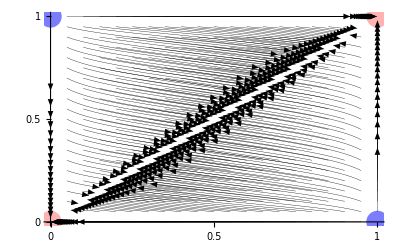

{{p11→0.,p12→1.},{p11→0.5,p12→0.5},{p11→1.,p12→0.}}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{{p11→0.,p12→1.},{p11→0.,p12→0.606563},{p11→0.,p12→0.980937},{p11→0.5,p12→0.5},{p11→1.,p12→0.},{p11→1.,p12→0.0190628},{p11→1.,p12→0.393437},{p11→0.714419,p12→0.},{p11→0.285581,p12→1.},{p11→0.311419,p12→0.991075},{p11→0.688581,p12→0.00892531}}

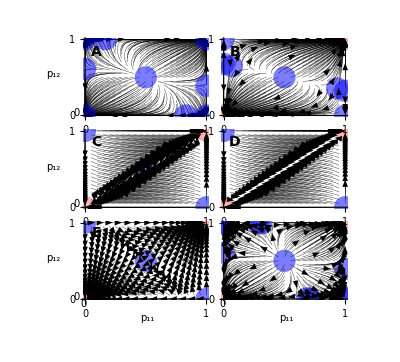

/Users/johnbunce/Desktop/Fig4.pdf

```mathematica
(*Figure 4: Field plots and numerically-solved equilibria*)

grp1freqs=Range[0,1,0.05]; (*plotting ranges, change step sizes to 0.1 to make it run faster*)
grp2freqs=Range[0,1,0.05];
tmaxfield=30;


(*A*******************************************majority resource control, a=0*)
coords={-100,-100}; (*initialize with junk*)

For    [x2=1,x2≤Length[grp2freqs],x2++,
For    [x1=1,x1≤Length[grp1freqs],x1++,

boundsim[
pg1init={grp1freqs[[x1]],1-grp1freqs[[x1]]},  (*group 1: norm 1, norm 2*)
pg2init={grp2freqs[[x2]],1-grp2freqs[[x2]]}, (*group 2: norm 1, norm 2*)

tmax =tmaxfield,

a=0, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];(*boundsim*)

coords=Join[coords,Append[{matg1all[[All,1]]},matg2all[[All,1]]]];

](*for x1*)
(*Print["Grp 2 freq: ",grp2freqs[[x2]]]*)
](*for x2*)

boundsolve[
a=0/10, (*prob of assorting on marker*)
m={1/10,1/10},(*proportion of each group that is visitors*)
d={{1,5/10},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={9/10,5/10},(*inter-ethnic coordination payoff bonus for each group*)
mu=5/10(*effect of a payoff difference on copying*)
];(*boundsolve*)


coords=coords[[3;;Length[coords]]]; (*delete first two junk rows*)
coords=Partition[coords,2];(*create sub-matrices of trajectories*)
coords//MatrixForm;

coords=Flatten[coords,1];
coords=Transpose[coords];
coords=Partition[coords,{tmaxfield,2}];
coords=Transpose[coords];
(*coords=Transpose[Partition[Transpose[Flatten[coords,1]],{tmaxfield,2}]];*)
coords//MatrixForm ;(*now a matrix of paired coordinates*)


plot0=ListLinePlot[coords[[9]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}}
]/.Line->Arrow;

plotmat=plot0;

For    [x3=2,x3≤Length[coords],x3++,

plotTemp=ListLinePlot[coords[[x3]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}},
TicksStyle->{White, Black},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0"},{0.5,"0.5"},{1,"1"}}} (*y axis, {0,0} is tick length*)
]/.Line->Arrow;

plotmat={plotmat,plotTemp};

](*for x3*)


points//MatrixForm; (*equilibria from boundarysolve function*)


equilibplot= ListPlot[
points,
(*PlotLabel->"Norm 1",*)
PlotStyle->{{PointSize[0.04],Blue, Opacity[0.3]}},
TicksStyle->{White, Black}, (*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0"},{0.5,"0.5"},{1,"1"}}} (*y axis, {0,0} is tick length*)
];


plotfielda=Show[equilibplot, plotmat];

(*
Labeled[plotfielda,
{"Group 1", "Group 2"},
{Bottom, Left}, RotateLabel -> True]
*)


(*B*******************************************majority resource control, a=0.5*)
coords={-100,-100}; (*initialize with junk*)

For    [x2=1,x2≤Length[grp2freqs],x2++,
For    [x1=1,x1≤Length[grp1freqs],x1++,

boundsim[
pg1init={grp1freqs[[x1]],1-grp1freqs[[x1]]},  (*group 1: norm 1, norm 2*)
pg2init={grp2freqs[[x2]],1-grp2freqs[[x2]]}, (*group 2: norm 1, norm 2*)

tmax =tmaxfield,

a=0.5, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];(*boundsim*)

coords=Join[coords,Append[{matg1all[[All,1]]},matg2all[[All,1]]]];

](*for x1*)
(*Print["Grp 2 freq: ",grp2freqs[[x2]]]*)
](*for x2*)

boundsolve[
a=5/10, (*prob of assorting on marker*)
m={1/10,1/10},(*proportion of each group that is visitors*)
d={{1,5/10},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={9/10,5/10},(*inter-ethnic coordination payoff bonus for each group*)
mu=5/10(*effect of a payoff difference on copying*)
];(*boundsolve*)


coords=coords[[3;;Length[coords]]]; (*delete first two junk rows*)
coords=Partition[coords,2];(*create sub-matrices of trajectories*)
coords//MatrixForm;

coords=Flatten[coords,1];
coords=Transpose[coords];
coords=Partition[coords,{tmaxfield,2}];
coords=Transpose[coords];
(*coords=Transpose[Partition[Transpose[Flatten[coords,1]],{tmaxfield,2}]];*)
coords//MatrixForm; (*now a matrix of paired coordinates*)


plot0=ListLinePlot[coords[[9]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}},
TicksStyle->{{White, Opacity[0]}, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
]/.Line->Arrow;

plotmat=plot0;

For    [x3=2,x3≤Length[coords],x3++,

plotTemp=ListLinePlot[coords[[x3]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}}
]/.Line->Arrow;

plotmat={plotmat,plotTemp};

](*for x3*)


points//MatrixForm; (*equilibria from boundarysolve function*)


equilibplot= ListPlot[
points,
(*PlotLabel->"Norm 1",*)
PlotStyle->{{PointSize[0.04],Blue, Opacity[0.3]}},
TicksStyle->{{White, Opacity[0]}, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];

(*points for undefined equilibria*)
missingplot= ListPlot[
{{0,0},{1,1}},
PlotStyle->{{PointSize[0.04],Red, Opacity[0.3]}},
TicksStyle->{{White, Opacity[0]}, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];


plotfieldb=Show[equilibplot,missingplot, plotmat];

(*
Labeled[plotfieldb,
{"Group 1", "Group 2"},
{Bottom, Left}, RotateLabel -> True]
*)


(*C*******************************************majority resource control, a=0.99*)
coords={-100,-100}; (*initialize with junk*)

For    [x2=1,x2≤Length[grp2freqs],x2++,
For    [x1=1,x1≤Length[grp1freqs],x1++,

boundsim[
pg1init={grp1freqs[[x1]],1-grp1freqs[[x1]]},  (*group 1: norm 0, norm 1*)
pg2init={grp2freqs[[x2]],1-grp2freqs[[x2]]}, (*group 2: norm 0, norm 1*)

tmax =tmaxfield,

a=0.99, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];(*boundsim*)

coords=Join[coords,Append[{matg1all[[All,1]]},matg2all[[All,1]]]];

](*for x1*)
(*Print["Grp 2 freq: ",grp2freqs[[x2]]]*)
](*for x2*)

boundsolve[
a=9.9/10, (*prob of assorting on marker*)
m={1/10,1/10},(*proportion of each group that is visitors*)
d={{1,5/10},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={9/10,5/10},(*inter-ethnic coordination payoff bonus for each group*)
mu=5/10(*effect of a payoff difference on copying*)
];(*boundsolve*)


coords=coords[[3;;Length[coords]]]; (*delete first two junk rows*)
coords=Partition[coords,2];(*create sub-matrices of trajectories*)
coords//MatrixForm;

coords=Flatten[coords,1];
coords=Transpose[coords];
coords=Partition[coords,{tmaxfield,2}];
coords=Transpose[coords];
(*coords=Transpose[Partition[Transpose[Flatten[coords,1]],{tmaxfield,2}]];*)
coords//MatrixForm; (*now a matrix of paired coordinates*)


plot0=ListLinePlot[coords[[9]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}},
TicksStyle->{White, Black},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0"},{0.5,"0.5"},{1,"1"}}} (*y axis, {0,0} is tick length*)
]/.Line->Arrow;

plotmat=plot0;

For    [x3=2,x3≤Length[coords],x3++,

plotTemp=ListLinePlot[coords[[x3]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}}
]/.Line->Arrow;

plotmat={plotmat,plotTemp};

](*for x3*)


points//MatrixForm; (*equilibria from boundarysolve function*)


equilibplot= ListPlot[
points,
(*PlotLabel->"Norm 1",*)
PlotStyle->{{PointSize[0.04],Blue, Opacity[0.3]}},
TicksStyle->{White, Black},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0"},{0.5,"0.5"},{1,"1"}}} (*y axis, {0,0} is tick length*)
];

missingplot= ListPlot[
{{0,0},{1,1}},
PlotStyle->{{PointSize[0.04],Red, Opacity[0.3]}},
TicksStyle->{Black, White},(*x, y*)
Ticks->{{{0,"0"},{0.5,"0.5"},{1,"1"}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];


plotfieldc=Show[equilibplot,missingplot, plotmat];

(*
Labeled[plotfieldc,
{"Group 1", "Group 2"},
{Bottom, Left}, RotateLabel -> True]
*)



(*D*******************************************majority resource control, a=1*)
coords={-100,-100}; (*initialize with junk*)

For    [x2=1,x2≤Length[grp2freqs],x2++,
For    [x1=1,x1≤Length[grp1freqs],x1++,

boundsim[
pg1init={grp1freqs[[x1]],1-grp1freqs[[x1]]},  (*group 1: norm 0, norm 1*)
pg2init={grp2freqs[[x2]],1-grp2freqs[[x2]]}, (*group 2: norm 0, norm 1*)

tmax =tmaxfield,

a=1, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];(*boundsim*)

coords=Join[coords,Append[{matg1all[[All,1]]},matg2all[[All,1]]]];

](*for x1*)
(*Print["Grp 2 freq: ",grp2freqs[[x2]]]*)
](*for x2*)

boundsolve[
a=1, (*prob of assorting on marker*)
m={1/10,1/10},(*proportion of each group that is visitors*)
d={{1,5/10},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={9/10,5/10},(*inter-ethnic coordination payoff bonus for each group*)
mu=5/10(*effect of a payoff difference on copying*)
];(*boundsolve*)


coords=coords[[3;;Length[coords]]]; (*delete first two junk rows*)
coords=Partition[coords,2];(*create sub-matrices of trajectories*)
coords//MatrixForm;

coords=Flatten[coords,1];
coords=Transpose[coords];
coords=Partition[coords,{tmaxfield,2}];
coords=Transpose[coords];
(*coords=Transpose[Partition[Transpose[Flatten[coords,1]],{tmaxfield,2}]];*)
coords//MatrixForm;(*now a matrix of paired coordinates*)


plot0=ListLinePlot[coords[[9]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}},
TicksStyle->{{White, Opacity[0]}, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
]/.Line->Arrow;

plotmat=plot0;

For    [x3=2,x3≤Length[coords],x3++,

plotTemp=ListLinePlot[coords[[x3]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}}
]/.Line->Arrow;

plotmat={plotmat,plotTemp};

](*for x3*)


points//MatrixForm; (*equilibria from boundarysolve function*)


equilibplot= ListPlot[
points,
(*PlotLabel->"Norm 1",*)
PlotStyle->{{PointSize[0.04],Blue, Opacity[0.3]}},
TicksStyle->{{White, Opacity[0]}, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];

missingplot= ListPlot[
{{0,0},{1,1}},
PlotStyle->{{PointSize[0.04],Red, Opacity[0.3]}},
TicksStyle->{{White, Opacity[0]}, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];

plotfieldd=Show[equilibplot,missingplot, plotmat];

(*
Labeled[plotfieldd,
{"Group 1", "Group 2"},
{Bottom, Left}, RotateLabel -> True]
*)



(*E*******************************************minority resource control, a=0.9*)
coords={-100,-100}; (*initialize with junk*)

For    [x2=1,x2≤Length[grp2freqs],x2++,
For    [x1=1,x1≤Length[grp1freqs],x1++,

boundsim[
pg1init={grp1freqs[[x1]],1-grp1freqs[[x1]]},  (*group 1: norm 0, norm 1*)
pg2init={grp2freqs[[x2]],1-grp2freqs[[x2]]}, (*group 2: norm 0, norm 1*)

tmax =tmaxfield,

a=0.9, (*prob of assorting on marker*)
m={0.1,0.1},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.1,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];(*boundsim*)

coords=Join[coords,Append[{matg1all[[All,1]]},matg2all[[All,1]]]];

](*for x1*)
(*Print["Grp 2 freq: ",grp2freqs[[x2]]]*)
](*for x2*)

boundsolve[
a=9/10, (*prob of assorting on marker*)
m={1/10,1/10},(*proportion of each group that is visitors*)
d={{1,5/10},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={1/10,5/10},(*inter-ethnic coordination payoff bonus for each group*)
mu=5/10(*effect of a payoff difference on copying*)
];(*boundsolve*)


coords=coords[[3;;Length[coords]]]; (*delete first two junk rows*)
coords=Partition[coords,2];(*create sub-matrices of trajectories*)
coords//MatrixForm;

coords=Flatten[coords,1];
coords=Transpose[coords];
coords=Partition[coords,{tmaxfield,2}];
coords=Transpose[coords];
(*coords=Transpose[Partition[Transpose[Flatten[coords,1]],{tmaxfield,2}]];*)
coords//MatrixForm; (*now a matrix of paired coordinates*)


plot0=ListLinePlot[coords[[9]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}},
TicksStyle->{Black, Black},(*x, y*)
Ticks->{{{0,"0"},{0.5,"0.5"},{1,"1"}},(*x axis*)
{{0,"0"},{0.5,"0.5"},{1,"1"}}} (*y axis, {0,0} is tick length*)
]/.Line->Arrow;

plotmat=plot0;

For    [x3=2,x3≤Length[coords],x3++,

plotTemp=ListLinePlot[coords[[x3]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}}
]/.Line->Arrow;

plotmat={plotmat,plotTemp};

](*for x3*)


points//MatrixForm; (*equilibria from boundarysolve function*)


equilibplot= ListPlot[
points,
(*PlotLabel->"Norm 1",*)
PlotStyle->{{PointSize[0.04],Blue, Opacity[0.3]}},
TicksStyle->{Black, Black},(*x, y*)
Ticks->{{{0,"0"},{0.5,"0.5"},{1,"1"}},(*x axis*)
{{0,"0"},{0.5,"0.5"},{1,"1"}}} (*y axis, {0,0} is tick length*)
];

missingplot= ListPlot[
{{0,0},{1,1}},
PlotStyle->{{PointSize[0.04],Red, Opacity[0.3]}},
TicksStyle->{Black, White},(*x, y*)
Ticks->{{{0,"0"},{0.5,"0.5"},{1,"1"}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];


plotfielde=Show[equilibplot,missingplot, plotmat];

(*
Labeled[plotfielde,
{"Group 1", "Group 2"},
{Bottom, Left}, RotateLabel -> True]

*)


(*F*******************************************minority homeland, a=0.7*)
coords={-100,-100}; (*initialize with junk*)

For    [x2=1,x2≤Length[grp2freqs],x2++,
For    [x1=1,x1≤Length[grp1freqs],x1++,

boundsim[
pg1init={grp1freqs[[x1]],1-grp1freqs[[x1]]},  (*group 1: norm 0, norm 1*)
pg2init={grp2freqs[[x2]],1-grp2freqs[[x2]]}, (*group 2: norm 0, norm 1*)

tmax =tmaxfield,

a=0.7, (*prob of assorting on marker*)
m={0.1,0},(*proportion of each group that is visitors*)
d={{1,0.5},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={0.9,0.5},(*inter-ethnic coordination payoff bonus for each group*)
mu=0.5(*effect of a payoff difference on copying*)
];(*boundsim*)

coords=Join[coords,Append[{matg1all[[All,1]]},matg2all[[All,1]]]];

](*for x1*)
(*Print["Grp 2 freq: ",grp2freqs[[x2]]]*)
](*for x2*)

boundsolve[
a=7/10, (*prob of assorting on marker*)
m={1/10,0},(*proportion of each group that is visitors*)
d={{1,5/10},{2,1}},
(*relative group sizes: how many times bigger the row group is than the column group*)
g={9/10,5/10},(*inter-ethnic coordination payoff bonus for each group*)
mu=5/10(*effect of a payoff difference on copying*)
];(*boundsolve*)


coords=coords[[3;;Length[coords]]]; (*delete first two junk rows*)
coords=Partition[coords,2];(*create sub-matrices of trajectories*)
coords//MatrixForm;

coords=Flatten[coords,1];
coords=Transpose[coords];
coords=Partition[coords,{tmaxfield,2}];
coords=Transpose[coords];
(*coords=Transpose[Partition[Transpose[Flatten[coords,1]],{tmaxfield,2}]];*)
coords//MatrixForm; (*now a matrix of paired coordinates*)


plot0=ListLinePlot[coords[[9]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}},
TicksStyle->{Black, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0"},{0.5,"0.5"},{1,"1"}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
]/.Line->Arrow;

plotmat=plot0;

For    [x3=2,x3≤Length[coords],x3++,

plotTemp=ListLinePlot[coords[[x3]] , 
(*PlotLabel->"Norm 1",*)
PlotRange->{{-0.01,1.01},{-0.01,1.01}},
BaseStyle->Arrowheads[{0.02,0.02,0.02,0.02}],
PlotStyle->{{Black, AbsoluteThickness[0.25]}}
]/.Line->Arrow;

plotmat={plotmat,plotTemp};

](*for x3*)


points//MatrixForm; (*equilibria from boundarysolve function*)


equilibplot= ListPlot[
points,
(*PlotLabel->"Norm 1",*)
PlotStyle->{{PointSize[0.04],Blue, Opacity[0.3]}},
TicksStyle->{Black, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0"},{0.5,"0.5"},{1,"1"}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];

missingplot= ListPlot[
{{0,0},{1,1}},
PlotStyle->{{PointSize[0.04],Red, Opacity[0.3]}},
TicksStyle->{Black, {White, Opacity[0]}},(*x, y*)
Ticks->{{{0,"0"},{0.5,"0.5"},{1,"1"}},(*x axis*)
{{0,"0",{0,0}},{0.5,"0.5",{0,0}},{1,"1",{0,0}}}} (*y axis, {0,0} is tick length*)
];


plotfieldf=Show[equilibplot,missingplot,plotmat];

(*
Labeled[plotfieldf,
{"Group 1", "Group 2"},
{Bottom, Left}, RotateLabel -> True]
*)


(****************************************assemble plots into Fieldplot Figure 4*)
Fig4=Panel[
GraphicsGrid[
{{plotfielda,plotfieldb},
{plotfieldc,plotfieldd},
{plotfielde,plotfieldf}
},

Spacings->{
{
Scaled[0.6],
Scaled[-0.1],
Scaled[0.2]
},
{
Scaled[0],
Scaled[0],
Scaled[0],
Scaled[0.6]
}
},

Frame->True,
FrameStyle->Directive[White],

Epilog->{
Inset[Style["A",Bold,14],{145,-45},Background->White],
Inset[Style["B",Bold,14],{480,-45},Background->White],
Inset[Style["C",Bold,14],{145,-265},Background->White],
Inset[Style["D",Bold,14],{480,-265},Background->White],
Inset[Style["E",Bold,14],{145,-485},Background->White],
Inset[Style["F",Bold,14],{480,-485},Background->White],
Inset[Style[Subscript[Style["p",Italic,10],Style["12",8]],Italic,10],{40,-100}],
Inset[Style[Subscript[Style["p",Italic,10],Style["12",8]],Italic,10],{40,-325}],
Inset[Style[Subscript[Style["p",Italic,10],Style["12",8]],Italic,10],{40,-545}],
Inset[Style[Subscript[Style["p",Italic,10],Style["11",8]],Italic,10],{268,-690}],
Inset[Style[Subscript[Style["p",Italic,10],Style["11",8]],Italic,10],{604,-690}],
Inset[Style["0",10],{97,-193}],
Inset[Style["0",10],{97,-415}],
Inset[Style["0",10],{97,-640}],
Inset[Style["0",10],{113,-657}],
Inset[Style["0",10],{450,-657}]
}
],
Appearance->"Frameless",
Background->White,
FrameMargins->{{0,0},{5,10}}
](*panel*)


(*Export["/Users/johnbunce/Desktop/Fig4.pdf",Fig4,"PDF"]*)
Export["~/Fig4.pdf",Fig4,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```